```mathematica
ff[rsqr_]:=Exp[-rsqr]
```

```mathematica
ff[x_,y_,e_] := ff[x^2+y^2-I e]
```

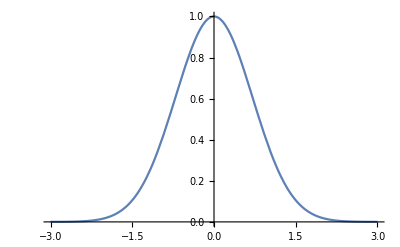

```mathematica
Plot[ff[x,0.,0.],{x,-3.,3.},PlotRange->{0.,1.},PlotPoints->50]
```